### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
constraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_]:={α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0}
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
Get["stableRegionsEq.mx"]
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

jOpt.9091768.comet-31-09

{0.101122,0.220957,0.779043,-0.433338,0.951835,0.481503,0.490764,0.89102,0.10898,0.896555,0.277149,-0.173704,0.300237,-0.120241,1.1026,1.57997,0.0784676,1.59373,0.700546,0.471354,-0.682046,0.566195,1.70604,-0.387171,-0.691094,1.32509,0.259118,0.106886,0.349989,-0.687283,0.973115,0.364179,-0.972096,1.90893,-0.681712,-0.255124,0.650011,0.687282,-0.973115,-0.364179,1.16115,-2.28018,0.244338,0.874691}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

15.6148

-Graphics3D-

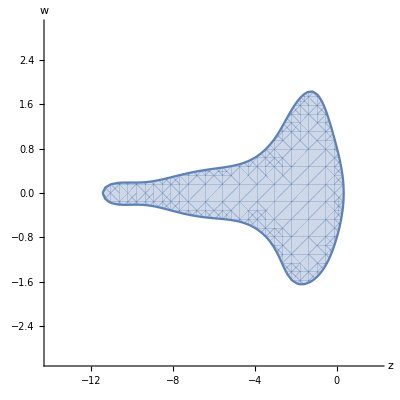

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.10112203114723364,0.22095675525925038,0.7790432447382618,-0.4333381449657492,0.9518354834732398,0.48150266133769853,0.4907643221759449,0.8910198306900541,0.10898016930994588,0.89655506206019,0.27714935051333506,-0.17370441257352506,0.3002368712321984,-0.12024145378859456,1.1025986988883951,1.5799741939682224,0.07846760935277848,1.5937345338076019,0.7005457315049121,0.47135437353058224,-0.6820461144198495,0.5661952695023388,1.70603882862755,-0.3871707566311114,-0.6910938391252304,1.3250895921176848,0.2591180581249546,0.10688619177269032,0.3499887705045853,-0.6872825081682153,0.9731149334006914,0.3641787994261447,-0.9720959709873365,1.9089313893896942,-0.6817115144985152,-0.2551239038124949,0.6500112469324765,0.6872824792993721,-0.9731149306362101,-0.36417879367621075,1.1611472255112696,-2.2801764851925257,0.24433825488405028,0.8746910104681979}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091771.comet-30-06 : SRIOpt2

{0.13804,0.576463,0.423537,0.459881,0.808486,-0.268367,0.454829,0.75197,0.24803,0.696169,0.346079,-0.0422476,0.0851329,1.02729,0.456589,1.72664,-0.460404,-0.962374,0.67441,-0.0737759,-0.498546,-0.562385,0.0236064,-0.895333,-0.149251,0.753226,0.691123,-0.295098,-0.455065,0.83472,0.379096,0.241249,-0.501467,0.919834,-0.255666,-0.162701,1.45507,-0.83472,-0.379096,-0.241249,-0.499859,0.916885,-1.4115,0.994475}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

18.6327

-Graphics3D-

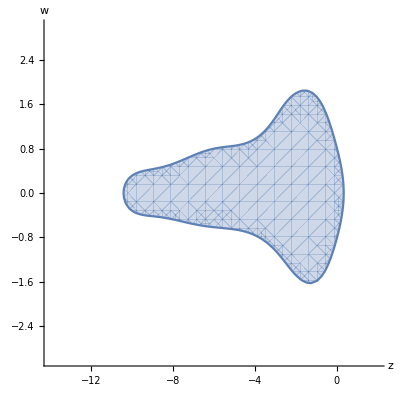

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.13803991182809405,0.5764629771061757,0.4235370228938241,0.45988142444172125,0.8084859191118128,-0.2683673489095204,0.45482884244918836,0.7519704601202507,0.24802953987974916,0.6961685917464052,0.3460790565637937,-0.04224764831019894,0.08513289389320751,1.0272930820405226,0.4565894293733811,1.7266402546369712,-0.46040416640520754,-0.9623742513556953,0.6744100174205603,-0.07377591084107533,-0.4985455217486592,-0.5623853411970345,0.023606441329882558,-0.8953332413687689,-0.14925077940925455,0.7532260416025327,0.6911225838401098,-0.2950978480741201,-0.4550650633914512,0.8347196075716,0.3790963153683881,0.24124914164997122,-0.5014671170389827,0.9198342527636846,-0.2556662881012024,-0.16270085567402398,1.4550650304633204,-0.8347196116875014,-0.37909625532888075,-0.24124916721822443,-0.4998591615011572,0.9168848205568053,-1.4115003346202473,0.994474673400943}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091788.comet-31-16

{0.0751979,-0.0694964,1.0695,-0.152225,1.09983,0.0523985,0.443289,0.992566,0.00743387,0.787515,0.250163,-0.0376781,0.108806,0.457702,0.354712,0.626973,1.26221,-0.397252,-0.6658,-1.08367,0.434309,3.71248,-0.15881,-1.70335,-0.741334,1.34227,-0.380532,0.779596,0.157962,-0.283742,0.908901,0.216878,0.941324,-1.69087,0.605146,0.144398,0.842038,0.283742,-0.908901,-0.216878,-1.56763,2.81588,-1.674,0.425752}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

13.1984

-Graphics3D-

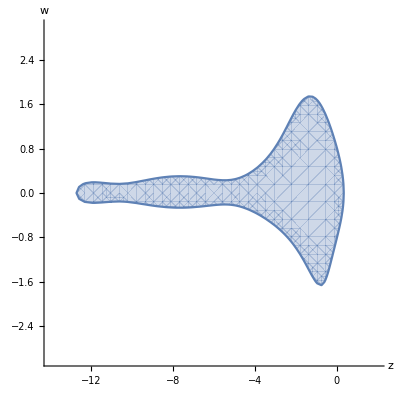

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.07519788885593696,-0.06949643927329126,1.0694964392681514,-0.1522251222812998,1.0998266313011555,0.05239849098014294,0.4432893980421528,0.9925661306103539,0.007433869389646297,0.7875149068373734,0.25016319442776613,-0.03767810126513897,0.1088062121063868,0.4577017766471385,0.3547124897943134,0.6269734317481137,1.262208306979323,-0.39725204936894987,-0.6657998109848107,-1.08367353263802,0.4343087675234363,3.712478464631237,-0.158810046896599,-1.7033531774688744,-0.7413336106671035,1.3422694398238284,-0.38053155726800675,0.7795957286734092,0.15796207948071708,-0.28374182014598404,0.9089014017198427,0.21687833951738097,0.9413242737406766,-1.6908682348962363,0.6051464035225309,0.1443975579842588,0.8420379278988441,0.2837418089595506,-0.9089013961726579,-0.21687833942011436,-1.5676321255689545,2.8158833702962753,-1.6740034356296143,0.42575219115133534}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091798.comet-31-06

{0.815722,0.758256,0.241744,1.08021,-0.155794,0.0755874,0.998955,0.621763,0.378236,0.276092,0.719136,0.00477193,0.316225,1.45944,-0.0503315,0.192252,0.780153,0.318374,-0.999479,0.601973,-3.39095,-0.343975,-1.64369,-1.78972,0.573333,-0.397949,0.519274,0.305341,-0.00242857,2.32559,-2.70505,1.38189,-0.00138205,1.32385,-2.70363,1.38116,1.00243,-2.32559,2.70505,-1.38189,-0.000419514,0.403217,-1.13163,0.728829}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

12.7219

-Graphics3D-

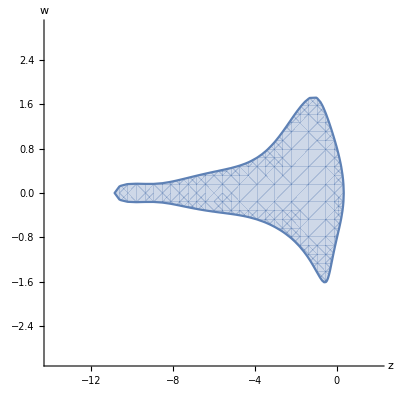

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.8157224826663422,0.7582558198605174,0.24174418013829102,1.0802061345741747,-0.15579352449406506,0.07558738991979685,0.9989550985995228,0.6217629874347799,0.3782364196665315,0.2760922375321842,0.7191357441658884,0.004771932884417922,0.3162245177340567,1.4594383108714917,-0.050331523593159816,0.19225215073872456,0.7801532062678923,0.3183737424551496,-0.9994786536266029,0.6019728082704031,-3.3909454995145167,-0.3439751257143109,-1.6436914529059263,-1.7897218096258694,0.5733329877204504,-0.3979486043419136,0.5192741457182737,0.30534146697132897,-0.0024285689423544565,2.325587519501506,-2.7050462560766713,1.3818872767193813,-0.0013820534114922266,1.32384843290311,-2.703630559589905,1.3811641938374317,1.002428572041987,-2.325587531203945,2.7050462753660964,-1.3818872865103562,-0.00041951404426384103,0.40321736178204987,-1.1316264923739447,0.7288286996863537}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

{0.138045,0.581836,0.418164,0.467002,0.80462,-0.271622,0.456055,0.755581,0.244419,0.698118,0.345328,-0.0434458,0.0885238,1.03178,0.456355,1.73078,-0.460897,-0.963751,0.675319,-0.0745281,-0.497837,-0.559191,0.0226966,-0.898493,-0.150369,0.754528,0.686995,-0.291154,-0.453157,0.833094,0.379284,0.240779,-0.499438,0.918179,-0.256138,-0.162602,1.45316,-0.833094,-0.379284,-0.240779,-0.497609,0.914816,-1.41021,0.993004}

{True,True,False,False,False,False,True,False,False,True,True,True,True,False,True,False,True,False,True,True,False,False,False,True,False}

18.9047

-Graphics3D-

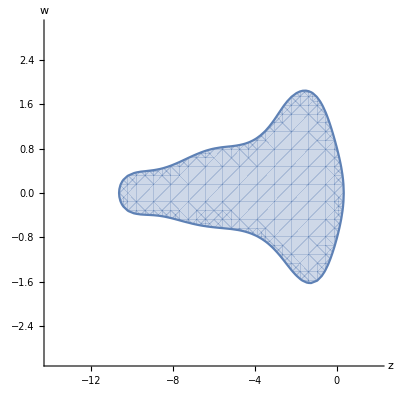

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.13804532298278663,0.5818361298250374,0.4181638701749618,0.4670018408674211,0.8046204792187386,-0.27162232008616016,0.45605532163856893,0.7555807846451692,0.24441921535482677,0.6981181143266059,0.3453277086024727,-0.04344582292908241,0.08852381537667678,1.0317752458971061,0.4563552922077882,1.73078280444124,-0.46089678470929774,-0.9637509618944188,0.6753186815412179,-0.07452812525785148,-0.49783736486149366,-0.5591906709928903,0.022696571806569924,-0.8984927888368557,-0.15036858140642623,0.7545275856696072,0.686995463807979,-0.2911544680711602,-0.45315689727309133,0.8330937231303951,0.3792843195533544,0.24077885458934192,-0.4994383733810986,0.9181786186154077,-0.25613778661003145,-0.16260245862427797,1.4531568972730915,-0.8330937231303933,-0.3792843195533583,-0.24077885458934023,-0.4976090683622265,0.9148155835648892,-1.4102107084476505,0.9930041932449877}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```